# Seminarska naloga

## Trikotnik

Nariši trikotnik, ki ima naslednje točke: A(1,0), B(3,2), C(4,1). Izračunaj tudi njihove kote.

```mathematica
trikotnik =Trikotnik[{1,0}, {3,2}, {4,1}]
```

Trikotnik[{1,0},{3,2},{4,1}]

```mathematica
Stranice[Trikotnik[A_, B_, C_]] := {Daljica[A, B], Daljica[B, C], Daljica[C, A]}
```

```mathematica
Koti[Trikotnik[A_, B_, C_]] := {Kot[C, A, B],Kot[A, B, C],Kot[B, C, A]}
```

```mathematica
SlikaOglisc[Trikotnik[A_, B_, C_]]:={Point[A], Point[B], Point[C]}
```

```mathematica
SlikaStranic[Trikotnik[A_, B_, C_]]:={Line[{A, B}], Line[{B, C}], Line[{C, A}] }
```

```mathematica
NarisiTrikotnik[t_Trikotnik]:=Graphics[{SlikaOglisc[t], SlikaStranic[t]}, AspectRatio->Automatic]
```

```mathematica
Stranice[trikotnik]
```

{Daljica[{1,0},{3,2}],Daljica[{3,2},{4,1}],Daljica[{4,1},{1,0}]}

```mathematica
Koti[trikotnik]
```

{Kot[{4,1},{1,0},{3,2}],Kot[{1,0},{3,2},{4,1}],Kot[{3,2},{4,1},{1,0}]}

```mathematica
SlikaOglisc[trikotnik]
```

{Point[{1,0}],Point[{3,2}],Point[{4,1}]}

```mathematica
SlikaStranic[trikotnik]
```

{Line[{{1,0},{3,2}}],Line[{{3,2},{4,1}}],Line[{{4,1},{1,0}}]}

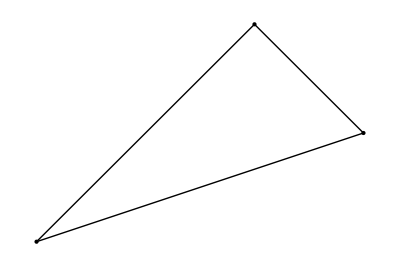

```mathematica
NarisiTrikotnik[trikotnik]
```

```mathematica
VelikostKota[Kot[A_,B_,C_]]:=ArcCos[(A-B).(C-B)/(Norm[A-B] Norm[C-B])]
```

```mathematica
koti = Koti[trikotnik]
```

{Kot[{4,1},{1,0},{3,2}],Kot[{1,0},{3,2},{4,1}],Kot[{3,2},{4,1},{1,0}]}

```mathematica
alfa = First[koti]
```

Kot[{4,1},{1,0},{3,2}]

```mathematica
FullSimplify[VelikostKota[alfa]]
```

ArcCos[2/(√5)]

```mathematica
gama = Last[koti]
```

Kot[{3,2},{4,1},{1,0}]

```mathematica
FullSimplify[VelikostKota[gama]]
```

ArcSec[√5]

```mathematica
beta = FullSimplify[180°- VelikostKota[alfa] - VelikostKota[gama]]
```

π/2

Pri nalogi sem moral prvo definirati posamezne točke, stranice, kote in ogljišča za kasnejše delo. Nato sem lahko šele narisal trikotnik. Pri nalogi sem moral še izračunati velikosti kotov. To sem naredil, tako da sem prvo definiral velikost kota, nato pa sem poklical posamezni kot. Pomagal sem si z funkcijo FullSimplify.

## Kvadratna funkcija

Imamo kvadratno funkcijo f(x)=x^2-2x-3.  Izračunajte ničli in zapišite presečišče grafa funkcije  f z osjo y. Narišite graf funkcije.

```mathematica
f[x_] := x^2 - 2*x - 3
```

```mathematica
začetna vrednost = f[0]
```

```mathematica
-3
```

```mathematica
ničle = Solve[f[x] == 0]
```

{{x→-1},{x→3}}

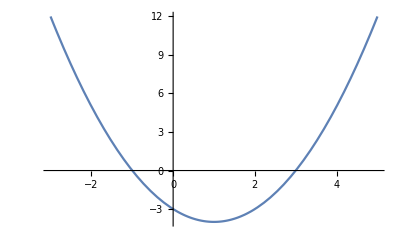

```mathematica
slika = Plot[f[x],{x,-3,5}]
```

Najprej sem zapisal funkcijo in nato ji izračunal ničle ter začetno vrednost. Nato pa sem moral še naslikati graf, kjer sem uporabil funkcijo Plot. Pri sliki sem upošteval, da so bistveni podatki okoli izhodišča, zato imam upoštevano razdaljo slike grafa od -3 do 5.

## Trigonometrija

Dana je funkcija f(x) =  2cosx - 1. Izračunajte ničle in ga narišite.

```mathematica
f[x_]:=2Cos[x]-1
```

```mathematica
zač_vr = Simplify[f[0]]
```

1

```mathematica
ničle = Reduce[f[x]==0]
```

Cos[x]==1/2

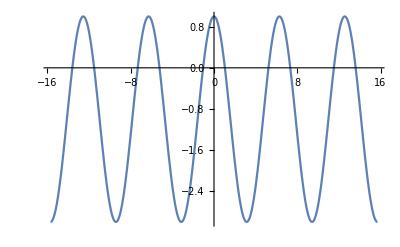

```mathematica
Plot[f[x], {x, -5Pi, 5Pi}]
```

Imel sem tudi nalogo z trigonometrijo, in sicer sem moral naristi graf sinusa. Bila je dana funkcija, kjer sem moral najprej izračunati začetno vrednost, nato pa še ničle funkcije. Kasneje sem uporabil funkcijo Plot, kjer sem določil meje za graf.

## Elipsa

Elipsa s središčem v izhodišču koordinatnega sistema ima naslednjo enačbo: x^2/3+y^2/2+3 z^2=2. Nariši elipso.

```mathematica
slika3 = ContourPlot3D[x^2/3+y^2/2+3 z^2==2,{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

Naloga je zahtevala, da narišem elipso v koordinatnem sistemu. Raje sem izbral, da sem jo narisal v 3D prostoru, ker se mi je zdelo bolj zanimivo. Za to sem uporabil funkcijo ContourPlot3D. V njo sem upisal funkcijo in za vsak parameter določil meje.